Name: Karan Sharma
College Roll No.: 2232191
University Roll No. : 22036563079
Class: BSc (Hons) Mathematics / Year 3 / Complex Analysis
Section: A

PRACTICAL 5 : Image of Half Plane under a given transformation

Q-1). Show that the image of the half plane Re[z]>1 under the linear transformation ω=f(z)=(-1+i)z+(-2+3i) is the half plane {2:v>u+7} where u=Re[ω] and v=Im[ω].

```mathematica
a=Region[HalfPlane[{{1,-5},{1,9}},{1,0}],Axes->True,AxesOrigin->{0,0,0},PlotRange->{{-7,6},{-5,9}},AxesLabel->{"Real Axes","Imaginary Axis"},PlotLabel->"Image in z-plane"]
```

```mathematica
Area[a](*not a finite rectangle*)
```

∞

```mathematica
z=x+ⅈ y
```

x+ⅈ y

```mathematica
ω=ComplexExpand[(-1+ⅈ)z+(-2+3ⅈ)]
```

-2-x+ⅈ (3+x-y)-y

TransformedRegion::reg: is not a correctly specified region.

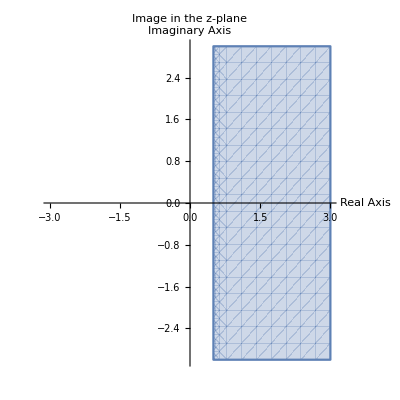
Region[TransformedRegion[-Graphics-,Function[p,{-2-p⟦1⟧-p⟦2⟧,3+p⟦1⟧-p⟦2⟧}]],Axes→True,PlotRange→{{-20,20},{-20,20}},AxesLabel→{Real Axis,Imaginary Axis},PlotLabel→Image in z-plane]

```mathematica
b=Region[TransformedRegion[a,Function[p,{-2-p[[1]]-p[[2]],3+p[[1]]-p[[2]]}]],Axes->True,PlotRange->{{-20,20},{-20,20}},AxesLabel->{"Real Axis","Imaginary Axis"},PlotLabel->"Image in z-plane"]
```

```mathematica
Area[b]
```